# 1. Data Ingestion & Orchestration

```mathematica
(*Automation through terminal and shell script to move CSV file to target folder*)
```

```mathematica
terminal[string_String]:=RunProcess[{"zsh","-i","-c",string}];
terminal["updateManu"];
```

# 2. Data Transformation & Validation

## Data & Sample

```mathematica
(*Import the data*)
```

```mathematica
data=Import["/Users/andrefreitas/andre/Manuela/manu.csv","RawData"];
```

```mathematica
(*Small sample of the data filtered by type "sleep"*)
```

```mathematica
{First[data],Select[data,Function[#[[1]]==="Sleep"]][[1;;3]]}//TableForm
```

Type | Start | End | Duration | Start Condition | Start Location | End Condition | Notes
Sleep
2026-01-24 18:28
2026-01-25 06:57
12:29



 | Sleep
2026-01-24 14:08
2026-01-24 14:53
00:45



 | Sleep
2026-01-24 10:23
2026-01-24 11:05
00:42



 |  |  |  |  |

## Variables1

```mathematica
(*Putting data into Tabular format and selecting only the relevant columns (first 4)*)
```

```mathematica
sleepTabular1=Tabular[Select[data,Function[#[[1]]==="Sleep"]],First[data]][[All,1;;4]]
```

```mathematica
(*adding a column 'Date' to indicate the day in which the sleeping started*)
```

```mathematica
sleepTabular2=TransformColumns[sleepTabular1,{"Type","Date"->Function[StringSplit[#Start," "]/.{a_,b_}->a]}]
```

```mathematica
(*Variable that list all days in string ISODate format from when sleeping data started to be collected (17/05/2025) up to the current day*)
```

```mathematica
dates=(DateString[#,"ISODate"]&/@DateRange[DateObject["2025-05-17"],Today,"Day"]);
```

{2025-05-17,2025-05-18,2025-05-19,2025-05-20,2025-05-21,2025-05-22,2025-05-23,2025-05-24,2025-05-25,2025-05-26,2025-05-27,2025-05-28,2025-05-29,2025-05-30,2025-05-31,2025-06-01,2025-06-02,2025-06-03,2025-06-04,2025-06-05,2025-06-06,2025-06-07,2025-06-08,2025-06-09,2025-06-10,2025-06-11,2025-06-12,2025-06-13,2025-06-14,2025-06-15,2025-06-16,2025-06-17,2025-06-18,2025-06-19,2025-06-20,2025-06-21,2025-06-22,2025-06-23,2025-06-24,2025-06-25,2025-06-26,2025-06-27,2025-06-28,2025-06-29,2025-06-30,2025-07-01,2025-07-02,2025-07-03,2025-07-04,2025-07-05,2025-07-06,2025-07-07,2025-07-08,2025-07-09,2025-07-10,2025-07-11,2025-07-12,2025-07-13,2025-07-14,2025-07-15,2025-07-16,2025-07-17,2025-07-18,2025-07-19,2025-07-20,2025-07-21,2025-07-22,2025-07-23,2025-07-24,2025-07-25,2025-07-26,2025-07-27,2025-07-28,2025-07-29,2025-07-30,2025-07-31,2025-08-01,2025-08-02,2025-08-03,2025-08-04,2025-08-05,2025-08-06,2025-08-07,2025-08-08,2025-08-09,2025-08-10,2025-08-11,2025-08-12,2025-08-13,2025-08-14,2025-08-15,2025-08-16,2025-08-17,2025-08-18,2025-08-19,2025-08-20,2025-08-21,2025-08-22,2025-08-23,2025-08-24,2025-08-25,2025-08-26,2025-08-27,2025-08-28,2025-08-29,2025-08-30,2025-08-31,2025-09-01,2025-09-02,2025-09-03,2025-09-04,2025-09-05,2025-09-06,2025-09-07,2025-09-08,2025-09-09,2025-09-10,2025-09-11,2025-09-12,2025-09-13,2025-09-14,2025-09-15,2025-09-16,2025-09-17,2025-09-18,2025-09-19,2025-09-20,2025-09-21,2025-09-22,2025-09-23,2025-09-24,2025-09-25,2025-09-26,2025-09-27,2025-09-28,2025-09-29,2025-09-30,2025-10-01,2025-10-02,2025-10-03,2025-10-04,2025-10-05,2025-10-06,2025-10-07,2025-10-08,2025-10-09,2025-10-10,2025-10-11,2025-10-12,2025-10-13,2025-10-14,2025-10-15,2025-10-16,2025-10-17,2025-10-18,2025-10-19,2025-10-20,2025-10-21,2025-10-22,2025-10-23,2025-10-24,2025-10-25,2025-10-26,2025-10-27,2025-10-28,2025-10-29,2025-10-30,2025-10-31,2025-11-01,2025-11-02,2025-11-03,2025-11-04,2025-11-05,2025-11-06,2025-11-07,2025-11-08,2025-11-09,2025-11-10,2025-11-11,2025-11-12,2025-11-13,2025-11-14,2025-11-15,2025-11-16,2025-11-17,2025-11-18,2025-11-19,2025-11-20,2025-11-21,2025-11-22,2025-11-23,2025-11-24,2025-11-25,2025-11-26,2025-11-27,2025-11-28,2025-11-29,2025-11-30,2025-12-01,2025-12-02,2025-12-03,2025-12-04,2025-12-05,2025-12-06,2025-12-07,2025-12-08,2025-12-09,2025-12-10,2025-12-11,2025-12-12,2025-12-13,2025-12-14,2025-12-15,2025-12-16,2025-12-17,2025-12-18,2025-12-19,2025-12-20,2025-12-21,2025-12-22,2025-12-23,2025-12-24,2025-12-25,2025-12-26,2025-12-27,2025-12-28,2025-12-29,2025-12-30,2025-12-31,2026-01-01,2026-01-02,2026-01-03,2026-01-04,2026-01-05,2026-01-06,2026-01-07,2026-01-08,2026-01-09,2026-01-10,2026-01-11,2026-01-12,2026-01-13,2026-01-14,2026-01-15,2026-01-16,2026-01-17,2026-01-18,2026-01-19,2026-01-20,2026-01-21,2026-01-22,2026-01-23,2026-01-24,2026-01-25}

## Functions

```mathematica
(*Function that adds column "Duration2" and "Time Range" which gives the duration of each sleeping session restricted to a specific day*)
```

```mathematica
f[date_String]:=TransformColumns[Select[sleepTabular2,Function[(StringSplit[#End," "]/.{a_,b_}->a)==date||#Date==date]],{"Duration2"->Function[If[(StringSplit[#End," "]/.{a_,b_}->a)!=date,DateObject[StringJoin[date," 23:59"]]-DateObject[#Start],If[(StringSplit[#Start," "]/.{a_,b_}->a)!=date,DateObject[#End]-DateObject[StringJoin[date," 00:01"]],DateObject[#End]-DateObject[#Start]],DateObject[#End]-DateObject[#Start]]],"TimeRange"->Function[If[(StringSplit[#End," "]/.{a_,b_}->a)!=date,(StringSplit[#Start," "]/.{a_,b_}->b)<>"-23:59",If[(StringSplit[#Start," "]/.{a_,b_}->a)!=date,"00:00-"<>(StringSplit[#End," "]/.{a_,b_}->b),(StringSplit[#Start," "]/.{a_,b_}->b)<>"-"<>(StringSplit[#End," "]/.{a_,b_}->b)]]]}]
```

```mathematica
(*example: the column "duration2" displays the amount of sleep only up until 23:59 on the 21/05/2025*)
```

```mathematica
f["2025-05-21"]
```

```mathematica
(*testing I can use the function to calculate total amount of sleep from 00:00 to 23:59 on any given day*)
```

```mathematica
f["2025-05-21"][[All,"Duration2"]]//Normal//Total
```

932 min

```mathematica
(*Function Gives the total amount of sleep for the inputed day, includint partial days*)
```

```mathematica
totalDaySleep[date_String]:=(f[date][[All,6]]//Normal//Total)/.Quantity[x_,"Minutes"]->Quantity[MixedMagnitude[{0,x}],MixedUnit[{"Hours","Minutes"}]]
```

```mathematica
(*Example*)
```

```mathematica
totalDaySleep["2026-01-25"]
```

6 56

```mathematica
(*Function gives last x days (including current day) as string "ISODate"*)
```

```mathematica
listOfDates[daysback_Integer]:=(DateString[#,"ISODate"]&/@DateRange[DatePlus[Today,-daysback],Yesterday,"Day"])
```

```mathematica
(*Example*)
```

```mathematica
listOfDates[7]
```

{2026-01-18,2026-01-19,2026-01-20,2026-01-21,2026-01-22,2026-01-23,2026-01-24}

```mathematica
(*Function Gives the total amount of sleep per day in the last "daysback"s not including current day*)
```

```mathematica
totalDaySleep2[daysback_Integer]:=Rule@@@Partition[Riffle[listOfDates[daysback],Map[totalDaySleep[#]&,listOfDates[daysback]]],2]
```

```mathematica
(*Example*)
```

```mathematica
totalDaySleep2[3]
```

{2026-01-22→13 52,2026-01-23→14 28,2026-01-24→14 6}

## Variables 2

Defining secondary feature set based on the primary variables established in Variables 1 subsection and on the functions established in the Functions section.

```mathematica
(*All data on total sleep (in hours and minutes) per day as an ASSOCIATION*)
```

```mathematica
sleepData=Rule@@@Partition[Riffle[dates,Map[totalDaySleep,dates]],2]
```

{2025-05-17→16 14,2025-05-18→14 42,2025-05-19→13 49,2025-05-20→13 13,2025-05-21→15 32,2025-05-22→12 36,2025-05-23→18 19,2025-05-24→12 24,2025-05-25→16 30,2025-05-26→13 3,2025-05-27→16 27,2025-05-28→13 20,2025-05-29→14 29,2025-05-30→15 22,2025-05-31→14 34,2025-06-01→16 21,2025-06-02→16 6,2025-06-03→13 42,2025-06-04→15 37,2025-06-05→16 40,2025-06-06→14 39,2025-06-07→19 24,2025-06-08→15 39,2025-06-09→14 26,2025-06-10→16 8,2025-06-11→14 47,2025-06-12→15 54,2025-06-13→15 51,2025-06-14→17 25,2025-06-15→15 8,2025-06-16→14 54,2025-06-17→13 47,2025-06-18→16 7,2025-06-19→15 7,2025-06-20→16 21,2025-06-21→17 43,2025-06-22→13 44,2025-06-23→16 3,2025-06-24→17 37,2025-06-25→13 23,2025-06-26→16 12,2025-06-27→17 3,2025-06-28→15 30,2025-06-29→13 46,2025-06-30→13 23,2025-07-01→15 52,2025-07-02→17 18,2025-07-03→14 41,2025-07-04→16 14,2025-07-05→14 17,2025-07-06→15 29,2025-07-07→14 18,2025-07-08→16 6,2025-07-09→15 57,2025-07-10→15 30,2025-07-11→14 52,2025-07-12→14 47,2025-07-13→14 29,2025-07-14→14 5,2025-07-15→14 14,2025-07-16→14 10,2025-07-17→15 25,2025-07-18→15 47,2025-07-19→14 38,2025-07-20→15 30,2025-07-21→16 0,2025-07-22→13 52,2025-07-23→15 58,2025-07-24→14 7,2025-07-25→13 59,2025-07-26→14 48,2025-07-27→14 53,2025-07-28→14 14,2025-07-29→14 11,2025-07-30→16 19,2025-07-31→13 45,2025-08-01→13 41,2025-08-02→16 49,2025-08-03→13 56,2025-08-04→13 12,2025-08-05→13 31,2025-08-06→15 15,2025-08-07→15 17,2025-08-08→13 22,2025-08-09→16 16,2025-08-10→13 44,2025-08-11→14 7,2025-08-12→13 8,2025-08-13→14 14,2025-08-14→14 19,2025-08-15→14 22,2025-08-16→14 56,2025-08-17→14 39,2025-08-18→13 42,2025-08-19→14 23,2025-08-20→15 18,2025-08-21→13 7,2025-08-22→13 5,2025-08-23→15 18,2025-08-24→13 21,2025-08-25→14 4,2025-08-26→14 32,2025-08-27→14 58,2025-08-28→13 56,2025-08-29→13 49,2025-08-30→13 37,2025-08-31→13 28,2025-09-01→14 35,2025-09-02→14 3,2025-09-03→14 51,2025-09-04→16 5,2025-09-05→14 13,2025-09-06→13 47,2025-09-07→15 5,2025-09-08→13 30,2025-09-09→14 28,2025-09-10→14 7,2025-09-11→12 59,2025-09-12→14 27,2025-09-13→14 8,2025-09-14→15 22,2025-09-15→13 33,2025-09-16→14 7,2025-09-17→13 24,2025-09-18→14 26,2025-09-19→13 49,2025-09-20→13 16,2025-09-21→15 12,2025-09-22→14 32,2025-09-23→13 56,2025-09-24→13 24,2025-09-25→14 15,2025-09-26→15 5,2025-09-27→13 17,2025-09-28→14 3,2025-09-29→13 35,2025-09-30→15 9,2025-10-01→15 21,2025-10-02→11 56,2025-10-03→14 27,2025-10-04→14 30,2025-10-05→13 13,2025-10-06→13 49,2025-10-07→13 10,2025-10-08→13 50,2025-10-09→13 43,2025-10-10→13 41,2025-10-11→13 57,2025-10-12→13 36,2025-10-13→12 36,2025-10-14→13 28,2025-10-15→13 3,2025-10-16→13 57,2025-10-17→13 2,2025-10-18→14 27,2025-10-19→14 20,2025-10-20→14 27,2025-10-21→13 10,2025-10-22→13 43,2025-10-23→14 0,2025-10-24→13 28,2025-10-25→13 44,2025-10-26→13 45,2025-10-27→13 58,2025-10-28→16 7,2025-10-29→13 58,2025-10-30→13 39,2025-10-31→14 11,2025-11-01→14 4,2025-11-02→14 6,2025-11-03→13 48,2025-11-04→13 23,2025-11-05→12 30,2025-11-06→12 46,2025-11-07→12 29,2025-11-08→12 38,2025-11-09→13 1,2025-11-10→13 24,2025-11-11→12 56,2025-11-12→14 24,2025-11-13→14 37,2025-11-14→14 2,2025-11-15→13 27,2025-11-16→13 21,2025-11-17→14 29,2025-11-18→13 6,2025-11-19→13 33,2025-11-20→13 25,2025-11-21→12 46,2025-11-22→13 32,2025-11-23→13 28,2025-11-24→13 23,2025-11-25→13 11,2025-11-26→13 39,2025-11-27→13 21,2025-11-28→12 30,2025-11-29→13 11,2025-11-30→13 29,2025-12-01→12 10,2025-12-02→13 20,2025-12-03→13 43,2025-12-04→13 23,2025-12-05→12 10,2025-12-06→13 12,2025-12-07→13 25,2025-12-08→12 58,2025-12-09→14 32,2025-12-10→12 42,2025-12-11→12 12,2025-12-12→12 43,2025-12-13→13 32,2025-12-14→13 13,2025-12-15→13 36,2025-12-16→13 46,2025-12-17→14 4,2025-12-18→13 32,2025-12-19→12 47,2025-12-20→13 25,2025-12-21→13 23,2025-12-22→12 55,2025-12-23→12 48,2025-12-24→12 54,2025-12-25→13 10,2025-12-26→12 46,2025-12-27→13 33,2025-12-28→12 30,2025-12-29→13 15,2025-12-30→13 31,2025-12-31→13 48,2026-01-01→12 54,2026-01-02→13 30,2026-01-03→13 54,2026-01-04→14 5,2026-01-05→14 1,2026-01-06→14 0,2026-01-07→14 20,2026-01-08→14 10,2026-01-09→12 23,2026-01-10→13 41,2026-01-11→13 28,2026-01-12→13 12,2026-01-13→13 5,2026-01-14→12 54,2026-01-15→13 58,2026-01-16→14 12,2026-01-17→13 59,2026-01-18→13 41,2026-01-19→13 50,2026-01-20→13 25,2026-01-21→14 5,2026-01-22→13 52,2026-01-23→14 28,2026-01-24→14 6,2026-01-25→6 56}

```mathematica
(*All data on total sleep per day as list of decimal hours*)
```

```mathematica
sleepData2=Drop[Function[UnitConvert[#,"Hours"]]/@Values[sleepData],-1]//N
```

{16.2333 h,14.7 h,13.8167 h,13.2167 h,15.5333 h,12.6 h,18.3167 h,12.4 h,16.5 h,13.05 h,16.45 h,13.3333 h,14.4833 h,15.3667 h,14.5667 h,16.35 h,16.1 h,13.7 h,15.6167 h,16.6667 h,14.65 h,19.4 h,15.65 h,14.4333 h,16.1333 h,14.7833 h,15.9 h,15.85 h,17.4167 h,15.1333 h,14.9 h,13.7833 h,16.1167 h,15.1167 h,16.35 h,17.7167 h,13.7333 h,16.05 h,17.6167 h,13.3833 h,16.2 h,17.05 h,15.5 h,13.7667 h,13.3833 h,15.8667 h,17.3 h,14.6833 h,16.2333 h,14.2833 h,15.4833 h,14.3 h,16.1 h,15.95 h,15.5 h,14.8667 h,14.7833 h,14.4833 h,14.0833 h,14.2333 h,14.1667 h,15.4167 h,15.7833 h,14.6333 h,15.5 h,16. h,13.8667 h,15.9667 h,14.1167 h,13.9833 h,14.8 h,14.8833 h,14.2333 h,14.1833 h,16.3167 h,13.75 h,13.6833 h,16.8167 h,13.9333 h,13.2 h,13.5167 h,15.25 h,15.2833 h,13.3667 h,16.2667 h,13.7333 h,14.1167 h,13.1333 h,14.2333 h,14.3167 h,14.3667 h,14.9333 h,14.65 h,13.7 h,14.3833 h,15.3 h,13.1167 h,13.0833 h,15.3 h,13.35 h,14.0667 h,14.5333 h,14.9667 h,13.9333 h,13.8167 h,13.6167 h,13.4667 h,14.5833 h,14.05 h,14.85 h,16.0833 h,14.2167 h,13.7833 h,15.0833 h,13.5 h,14.4667 h,14.1167 h,12.9833 h,14.45 h,14.1333 h,15.3667 h,13.55 h,14.1167 h,13.4 h,14.4333 h,13.8167 h,13.2667 h,15.2 h,14.5333 h,13.9333 h,13.4 h,14.25 h,15.0833 h,13.2833 h,14.05 h,13.5833 h,15.15 h,15.35 h,11.9333 h,14.45 h,14.5 h,13.2167 h,13.8167 h,13.1667 h,13.8333 h,13.7167 h,13.6833 h,13.95 h,13.6 h,12.6 h,13.4667 h,13.05 h,13.95 h,13.0333 h,14.45 h,14.3333 h,14.45 h,13.1667 h,13.7167 h,14. h,13.4667 h,13.7333 h,13.75 h,13.9667 h,16.1167 h,13.9667 h,13.65 h,14.1833 h,14.0667 h,14.1 h,13.8 h,13.3833 h,12.5 h,12.7667 h,12.4833 h,12.6333 h,13.0167 h,13.4 h,12.9333 h,14.4 h,14.6167 h,14.0333 h,13.45 h,13.35 h,14.4833 h,13.1 h,13.55 h,13.4167 h,12.7667 h,13.5333 h,13.4667 h,13.3833 h,13.1833 h,13.65 h,13.35 h,12.5 h,13.1833 h,13.4833 h,12.1667 h,13.3333 h,13.7167 h,13.3833 h,12.1667 h,13.2 h,13.4167 h,12.9667 h,14.5333 h,12.7 h,12.2 h,12.7167 h,13.5333 h,13.2167 h,13.6 h,13.7667 h,14.0667 h,13.5333 h,12.7833 h,13.4167 h,13.3833 h,12.9167 h,12.8 h,12.9 h,13.1667 h,12.7667 h,13.55 h,12.5 h,13.25 h,13.5167 h,13.8 h,12.9 h,13.5 h,13.9 h,14.0833 h,14.0167 h,14. h,14.3333 h,14.1667 h,12.3833 h,13.6833 h,13.4667 h,13.2 h,13.0833 h,12.9 h,13.9667 h,14.2 h,13.9833 h,13.6833 h,13.8333 h,13.4167 h,14.0833 h,13.8667 h,14.4667 h,14.1 h}

# Insights & Visual Monitoring

## Total Hours per day

```mathematica
(*Function to manually calculate the total amount of sleep in a day, for partial days calculations*)
```

```mathematica
manualSleeping[hours_List,minutes_List]:=Quantity[MixedMagnitude[{Total[Join[hours,{IntegerPart[Total[minutes]/60]}]],FractionalPart[Total[minutes]/60]*60}],MixedUnit[{"Hours","Minutes"}]]
```

```mathematica
(*Example*)
```

```mathematica
(*2026-01-24*)
```

```mathematica
manualSleeping[{1,4},{23,34}]
```

5 57

```mathematica
(*Total sleep in current day - Almost always partial*)
```

```mathematica
totalDaySleep[DateString[Today,"ISODate"]]
```

6 56

```mathematica
(*Total sleep per day from the last 8 days*)
```

```mathematica
totalDaySleep2[7]
```

{2026-01-18→13 41,2026-01-19→13 50,2026-01-20→13 25,2026-01-21→14 5,2026-01-22→13 52,2026-01-23→14 28,2026-01-24→14 6}

```mathematica
(*Avarege sleep from the last 7 days*)
```

```mathematica
((Mean[
UnitConvert[#,"Minutes"]&/@
([[All,2]])]
//N)
/60.0)/.Quantity[a_,"Minutes"]:>Quantity[MixedMagnitude[{IntegerPart[a],IntegerPart[FractionalPart[a]*60]}],MixedUnit[{"Hours","Minutes"}]]
```

13 55

## Naps per day

```mathematica
(*tracking the number of naps (under 120 min) per day*)
```

```mathematica
Function[Length[Select[f[#],Function[#Duration2<120]]]]/@dates
```

{8,8,15,11,8,9,5,8,10,10,7,8,9,10,11,9,6,11,11,12,9,8,8,13,8,10,12,8,8,8,9,8,7,8,5,9,9,6,6,11,8,7,8,8,7,4,6,10,6,5,8,5,5,6,6,5,6,6,6,5,6,4,6,5,4,6,5,2,5,5,5,3,5,5,6,5,7,2,8,7,4,2,4,4,4,5,4,4,3,6,3,6,3,4,5,4,5,6,4,6,3,3,4,3,3,4,5,4,6,4,3,4,4,7,5,4,6,5,3,5,5,5,5,5,7,3,5,3,5,5,4,3,1,4,5,5,5,4,5,3,4,4,3,4,4,4,3,3,3,5,6,8,4,4,3,4,4,7,3,4,3,5,4,4,4,3,4,2,3,5,3,4,5,3,3,5,5,4,3,3,4,4,4,4,3,5,5,4,3,3,4,3,4,4,5,4,3,5,5,3,7,8,5,5,3,4,3,4,5,4,3,5,3,4,3,6,3,4,4,3,3,4,3,3,3,5,4,4,4,5,5,1,3,2,3,3,2,3,3,4,3,3,3,2,3,3,3,2,4,2,2,2,4,0}

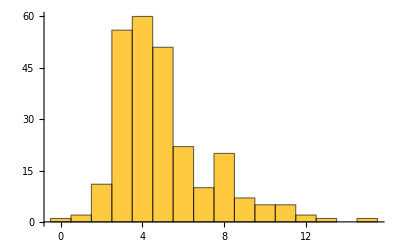

```mathematica
Histogram[]
```

## Distribution of Naps along specific days

```mathematica
barChartSleep[date_String]:=BarChart[f[date][[All,"Duration2"]]//QuantityMagnitude//Normal//Reverse,ChartLabels->(f[date][[All,"TimeRange"]]//Normal//Reverse)]
```

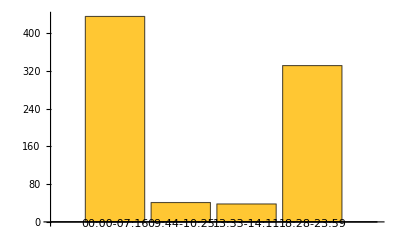
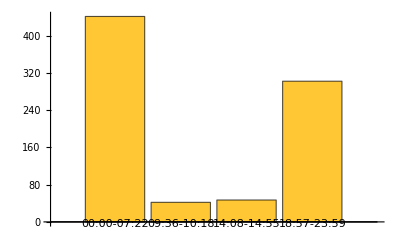
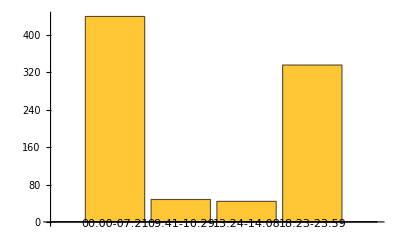
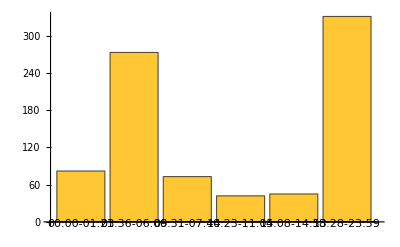

```mathematica
barChartSleep[#]&/@listOfDates[4]
```

## Moving average total hours per day

```mathematica
(*Moving average for 7 days agains raw data*)
```

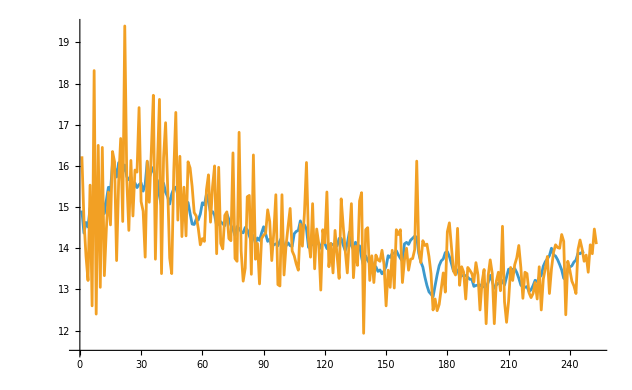

```mathematica
ListLinePlot[{MovingAverage[sleepData2,7],sleepData2}]
```

```mathematica
(*Moving average only*)
```

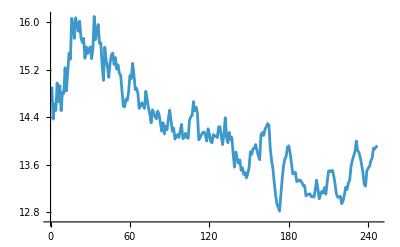

```mathematica
ListLinePlot[MovingAverage[sleepData2,7]]
```

```mathematica
(*Fitting the data with ListFitPlot[]*)
```

```mathematica
ListFitPlot[sleepData2[[1;;-2]],PlotRange->{Automatic,{12,20}}]
```

-Graphics-